```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
graphic={FaceForm[White],Polygon/@Coor/@Δ/@#1}&@FullInflate[starseed,9]
```

{FaceForm[-Graphics-],{Polygon[{{-1.61803,0},{-1.61397,-0.0125117},{-1.60081,-0.0125117},{-1.60488,0}}],Polygon[{{-1.61803,0},{-1.61397,0.0125117},{-1.60081,0.0125117},{-1.60488,0}}],33991,Polygon[{{1.30902,0.951057},{1.29837,0.958789},{1.28773,0.951057},{1.29837,0.943324}}],Polygon[{{1.30902,0.951057},{1.31308,0.938545},{1.30244,0.930812},{1.29837,0.943324}}]}}
 |  |  |  |

```mathematica
Show[{Graphics[{EdgeForm[Black],graphic},PlotRange->{{-2,2},{-2,2}}],Graphics[Translate[{Opacity[0.3],EdgeForm[Gray],graphic},0.5Dynamic@MousePosition["Graphics"]]]}]
```

-Graphics-

```mathematica
Mul
```

```mathematica
Translate[{Opacity[0.3],graphic},{0.5,0}]
```

Translate[{Opacity[0.3],{EdgeForm[-Graphics-],{{-Graphics-,Polygon[{{-1.56231,0},{-1.54508,0.0530006},{-1.52786,0},{-1.54508,-0.0530006}}]},{-Graphics-,Polygon[{{-1.54508,-0.0530006},{-1.60081,-0.0530006},{-1.61803,0},{-1.56231,0}}]},1921,{-Graphics-,Polygon[{{1.28115,-0.8653},{1.32624,-0.898056},{1.30902,-0.951057},{1.26393,-0.9183}}]},{-Graphics-,Polygon[{{1.28115,0.8653},{1.32624,0.898056},{1.30902,0.951057},{1.26393,0.9183}}]}}}},{0.5,0}]
 |  |  |  |

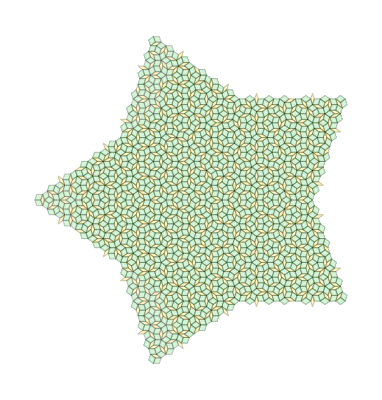

```mathematica
Graphics[{Opacity[0.2],graphic}]
```

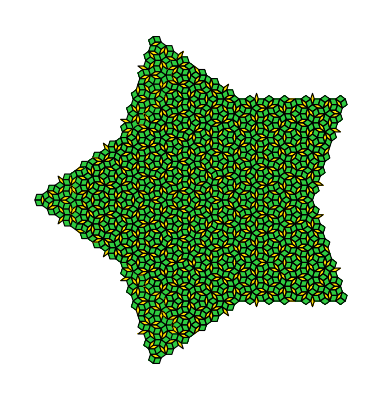

```mathematica
Graphics[Translate[{EdgeForm[Black],Transpose[{((If[Last[#1]=="fat",NiceGreen,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}&@FullInflate[starseed,6],{1,0}]]
```

```mathematica
Opacity
```

```mathematica
ImageMultiply[Graphics[Translate[{EdgeForm[Black],Transpose[{((If[Last[#1]=="fat",NiceGreen,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}&@FullInflate[starseed,6],{1,0}]],Graphics[Translate[{EdgeForm[Black],Transpose[{((If[Last[#1]=="fat",NiceGreen,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}&@FullInflate[starseed,6],{1,0}]]]
```

-Graphics-